$Aborted

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 3 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 4 Particles insertions

> Top. 1 aebe\cede\0.m, 0 diagrams

> Top. 2 aebe\cfdf\ef.m, 0 diagrams

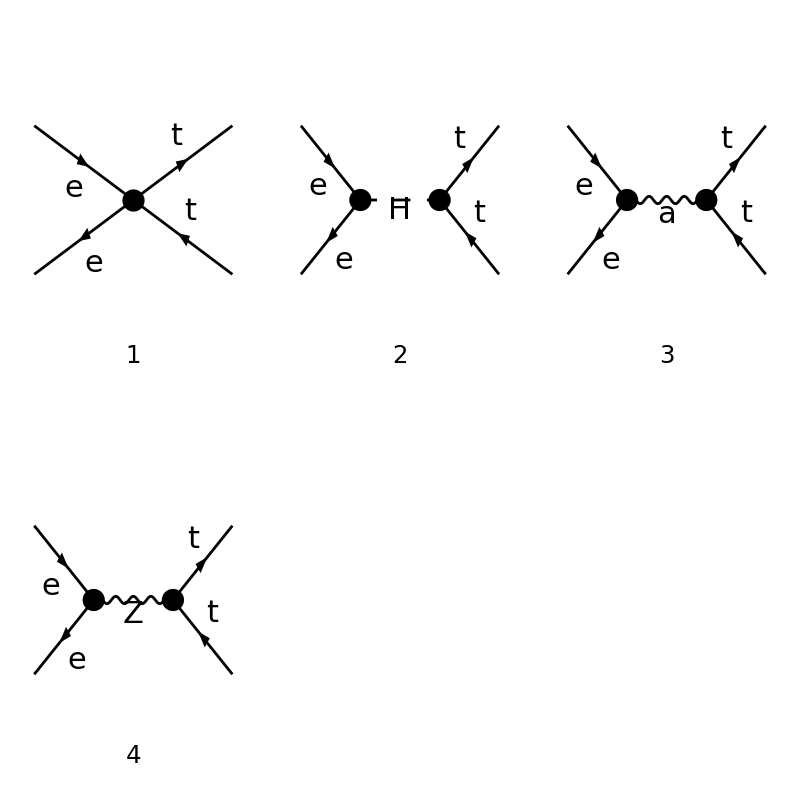

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 3 Particles amplitudes

in total: 4 Particles amplitudes

```mathematica
$LoadAddOns={"FeynArts"};(*hola*)
<<FeynCalc`;
SetOptions[FourVector, FeynCalcInternal -> False];
$FeynArtsModelPath=Append["...\\AppData\\Roaming\\Wolfram\\Applications\\FeynCalc\\FeynArts\\Models"];

(*----Catálogo de partículas (manual)----*)particleCatalog=<|"Leptones"->{F[2,{1}]->"e-",-F[2,{1}]->"e+",F[2,{2}]->"μ-",-F[2,{2}]->"μ+",F[2,{3}]->"τ-",-F[2,{3}]->"τ+"},"Neutrinos"->{F[1,{1}]->"νe", -F[1,{1}]->"νˉe", F[1,{2}]->"νμ", -F[1,{2}]->"νˉμ", F[1,{3}]->"ντ", -F[1,{3}]->"νˉτ"},"Quarks"->{F[3,{1}]->"u",-F[3,{1}]->"ū",F[3,{2}]->"c",-F[3,{2}]->"c̄",F[4,{1}]->"d",-F[4,{1}]->"d̄",F[4,{2}]->"s",-F[4,{2}]->"s̄",F[30]->"t",-F[30]->"t̄",F[40]->"b",-F[40]->"b̄"},"Vectores"->{V[1]->"γ", V[2]->"Z", V[3]->"W+", -V[3]->"W-", V[4]->"g"},"Escalares"->{S[1]->"H",S[2]->"G0", S[3]->"G+",-S[3]->"G-"},"Fantasmas"->{U[1]->"ghA", U[2]->"ghZ", U[31]->"ghWp", U[32]->"ghWm", U[4]->"ghG"}|>;

menuRules[cat_]:=Prepend[(#[[1]]->#[[2]])&/@particleCatalog[cat],"—"->None];

ClearAll[DiagramUIManualCatalog];

ClearAll[WithPrintCapture];
SetAttributes[WithPrintCapture,HoldFirst];
WithPrintCapture[expr_]:=Module[{res,prints},{res,prints}=Reap[Block[{Print},Print[x___]:=Sow[Row[{x}],"prints"];expr],"prints"];
{res,If[Length[prints]>=2,prints[[2,1]],{}]}];

ClearAll[quietEval];
SetAttributes[quietEval,HoldFirst];
quietEval[expr_]:=Quiet@Check[expr,$Failed];

Get["C:\\Users\\ruben\\AppData\\Roaming\\Wolfram\\Applications\\FeynCalc\\FeynArts\\Models\\\\SMEFTsimtopU3l.pars"];
coefNamesExt=First/@M$ExtParams;
coefNamesInt=First/@M$IntParams;
WCext=DeleteCases[coefNamesExt, aS | Gf | LambdaSMEFT | linearPropCorrections | MW | ymb | ymc | ymdo | yme | ymm | yms | ymt | ymtau | ymup];
WCint=DeleteCases[coefNamesInt, yup | yc | ydo | ys | yt | yb | MWsm | aEW | vevhat | lam | dkH | cth |dMH2 | G | ee | ye | ym | ytau | dGf | vevT | barlam | vev | sth2 | sth | dMZ2 | gw | g1 | dg1 | dgw | gwsh | g1sh | propCorr | MZ1 | MW1 | MH1 | MT1 | WZ1 | WW1 | WH1 | WT1 | dWZ | dWW | dWH | dWT | yt0 | yb0 | gHgg1 | gHgg2 | gHgg3 | gHgg4 | gHgg5 | gHaa | gHza ];
WC1=Join[WCext,WCint];
WC2=DeleteDuplicates[WC1];
wcQ[x_] := MemberQ[WC2, x];

(*Toggles para las reglas de simetría*)
useCpRules=False;
useRealRules=False;
useScalarTensorRules=False;
useEWLeptonRules=False;
useLinearWCRules=False;

DiagramUIManualCatalog[]:=DynamicModule[{
(*modelo*)
modelName="SMEFTsimtopU3l",genName="SMEFTsimtopU3l",
(*opciones físicas*)
insertion={Particles},loopOrder=0,
(*proceso*)
nIn=2,nOut=2,catInList=ConstantArray["Leptones",6],catOutList=ConstantArray["Quarks",6],pickIn=ConstantArray[None,6],pickOut=ConstantArray[None,6],
(*estado*)
running=False,statusDiag="Al ser la primera vez que genere los diagramas, debe pulsar dos veces para que cargue el modelo.",statusAmp="Listo.",logDiags={},
(*diagramas*)
diags=None,paintImg=None,paintG=None,
(*amplitud*)
ampFA=None,ampFC=None,showAmp=False,

        (*amplitud postprocesada*)
 ampFCproc=None,
wcResult={},
WC4={},
WilsonListSym={},
ampSymSelected=0,
showWCs=False,
statusWCs="Listo",
ampTmpSimp=None
},

(*Reglas para los WCs*)

cpRules = {
  (* todos los coeficientes imaginarios a 0 *)
  s_Symbol /; StringEndsQ[SymbolName[s], "Im"] :> 0,
  (* todos los "tilde" a 0 *)
  s_Symbol /; StringEndsQ[SymbolName[s], "til"] :> 0
};
realRules = {
  ComplexConjugate[s_Symbol] /; wcQ[s] :> s
};
scalarTensorPrefixes = {"cleQt", "clebQ", "cledj", "cleju"};

scalarTensorRules = Thread[
  Select[WC2,
    With[{n = SymbolName[#]},
      AnyTrue[scalarTensorPrefixes, StringStartsQ[n, #] &]
    ] &
  ] -> 0
];

keep2q2l = {cQl1, cQl3, cQe, ctl, cbl, cte};

ewLeptonToZero =
  Select[WC2,
    With[{n = SymbolName[#]},
      (
        StringStartsQ[n, "ce"] || StringStartsQ[n, "cl"] ||
        MemberQ[{"cHe", "cHl1", "cHl3"}, n]
      )
      && !MemberQ[keep2q2l, #]
    ] &
  ];

ewInputToZero = {cHbox, cHDD, cHWB};

ewLeptonRules = Thread[DeleteDuplicates@Join[ewInputToZero, ewLeptonToZero] -> 0];

linearWCRules = {
  a_ b_ /; wcQ[a] && wcQ[b] :> 0
};

applySelectedSymmetries[expr_]:=Module[{tmp=expr},If[useCpRules,tmp=tmp//.cpRules];
If[useRealRules,tmp=tmp//.realRules];
If[useLinearWCRules,tmp=tmp//.linearWCRules];
If[useScalarTensorRules,tmp=tmp//.scalarTensorRules];
If[useEWLeptonRules,tmp=tmp//.ewLeptonRules];
Simplify[tmp]];



 Column[{

(* ===================== BLOQUE 1: DIAGRAMAS =====================*)

Style["Generador de diagramas",16,Bold],
Grid[
{{"Model",InputField[Dynamic[modelName],String,FieldSize->22],"GenericModel",InputField[Dynamic[genName],String,FieldSize->22]},{"InsertionLevel",PopupMenu[Dynamic[insertion],{{Particles}->"{Particles}",{Classes}->"{Classes}"}],"LoopOrder",PopupMenu[Dynamic[loopOrder],{0->"0 (árbol)",1->"1 (1-loop)"}]}},Alignment->Left,Spacings->{2,1}
],
Delimiter,
Grid[
{{"# Entrantes (nIn):",SetterBar[Dynamic[nIn],Range[1,4]]},{"# Salientes (nOut):",SetterBar[Dynamic[nOut],Range[1,6]]}},Alignment->Left,Spacings->{2,1}
],
(* =====Entrantes=====*)
Style["Entrantes",12,Bold],Dynamic[Grid[Table[With[{k=i},{"in["<>ToString[k]<>"]",PopupMenu[Dynamic[catInList[[k]],(catInList[[k]]=#;pickIn[[k]]=None)&],Thread[Keys[particleCatalog]->Keys[particleCatalog]],FieldSize->12],PopupMenu[Dynamic[pickIn[[k]]],menuRules[catInList[[k]]],FieldSize->45]}],{i,1,nIn}],Alignment->Left,Spacings->{1.5,1}],TrackedSymbols:>{nIn,catInList,pickIn}],
Spacer[8],
(* =====Salientes=====*)
Style["Salientes",12,Bold],Dynamic[Grid[Table[With[{k=i},{"out["<>ToString[k]<>"]",PopupMenu[Dynamic[catOutList[[k]],(catOutList[[k]]=#;pickOut[[k]]=None)&],Thread[Keys[particleCatalog]->Keys[particleCatalog]],FieldSize->12],PopupMenu[Dynamic[pickOut[[k]]],menuRules[catOutList[[k]]],FieldSize->45]}],{i,1,nOut}],Alignment->Left,Spacings->{1.5,1}],TrackedSymbols:>{nOut,catOutList,pickOut}],
Spacer[10],Row[
{Button[
Dynamic[If[running,"Generando…","Generar diagramas"]],
If[
running,Null,
Module[
{inList,outList,top,tmp,img},running=True;
(*limpia prints/messages de FeynArts*)
NotebookDelete@Cells[CellStyle->"Print"];
NotebookDelete@Cells[CellStyle->"Message"];
(*resetea preview anterior*)
diags=None;
paintImg=None;
inList=Take[pickIn,nIn];
outList=Take[pickOut,nOut];
If[
MemberQ[inList,None]||MemberQ[outList,None],statusDiag=Style["Selecciona todas las partículas en in y out.",Red];
running=False;Return[];
];
statusDiag="CreateTopologies + InsertFields…";
tmp=TimeConstrained[Quiet@Check[top=CreateTopologies[loopOrder,nIn->nOut];
InsertFields[top,inList->outList,InsertionLevel->insertion,Model->modelName,GenericModel->genName],$Failed],60,$TimedOut];
If[
tmp===$TimedOut||tmp===$Failed||tmp===$Aborted,statusDiag=Style["Fallo/timeout generando diagramas. Revisa el proceso/modelo.",Red];
running=False;Return[];
];
diags=tmp;
statusDiag="Pintando…";

paintG=TimeConstrained[Quiet@Check[Paint[diags,Numbering->Simple,SheetHeader->None,ColumnsXRows->{3,2},ImageSize->800],$Failed],30,$TimedOut];

If[paintG===$TimedOut||paintG===$Failed,paintG=None;
paintImg=None;
statusDiag="Diagramas generados (sin preview).",paintImg=Quiet@Check[Rasterize[paintG,"Image"],$Failed];
If[paintImg===$Failed,paintImg=None];
statusDiag=Style["Diagramas generados. (salen al final)", Green]];
running=False;
]
],
Method->"Queued"
],
Spacer[10],
Button[
"Reset/Limpiar",NotebookDelete@Cells[CellStyle->"Print"];
NotebookDelete@Cells[CellStyle->"Message"];
diags=None;
paintImg=None;
paintG=None;
pickIn=ConstantArray[None,6];
pickOut=ConstantArray[None,6];
statusDiag=Style["Diagramas reseteados.",Orange];
],Spacer[10],
(* ======Exportar diagramas a PDF======*)
Button[
"Exportar diagramas a PDF",
Module[
{path,g},If[diags===None,statusDiag=Style["No hay diagramas para exportar (genera primero).",Red];
Return[];];
path=SystemDialogInput["FileSave","diagramas.pdf"];
If[path===$Canceled,Return[]];
statusDiag=Style["Exportando a PDF…",Yellow];
g=Paint[diags,Numbering->Simple,SheetHeader->None,ColumnsXRows->{3,2},ImageSize->800];
Quiet@Check[Export[path,g,"PDF"],statusDiag=Style["Error exportando a PDF.",Red];
Return[];];
statusDiag=Style["PDF exportado: "<>ToString[path],Green];
],Method->"Queued"
]}
],Delimiter,Dynamic[statusDiag],Spacer[15],
Dynamic[If[paintG===None&&paintImg===None,Column[{Style["Vista previa de los diagramas:",12,Bold],If[paintImg===None,paintImg,paintG]}], Nothing],TrackedSymbols:>{paintG,paintImg}],
(*Debug útil:VERIFICAR que son F[...]/V[...] y no strings*)Dynamic[Column[{Style["(Debug) in/out internos:",11,Italic],"in  = "<>ToString[Take[pickIn,nIn],InputForm],"out = "<>ToString[Take[pickOut,nOut],InputForm]}],TrackedSymbols:>{pickIn,pickOut,nIn,nOut}],
Column[{

(* ===================== BLOQUE 2: Amplitudes =====================*)

Style["Generador de amplitudes", 16, Bold],
Row[{Checkbox[Dynamic[useCpRules]]," Simetría CP ",Checkbox[Dynamic[useRealRules]]," Coeficientes Reales ",Checkbox[Dynamic[useScalarTensorRules]]," Scalar Tensor Rules ",Checkbox[Dynamic[useEWLeptonRules]]," Lepton Rules ",Checkbox[Dynamic[useLinearWCRules]]," Linear WCs "}],
Spacer[10],
Grid[
{{"Visualizar la amplitud:",PopupMenu[Dynamic[showAmp],{True->"Sí",False->"No"}]}},
Alignment->Left,Spacings->{2,1}
],
Spacer[10],
Button[
"Calcular amplitud",Module[{tmpFA,tmpFC},
If[diags===None,statusAmp=Style["Primero genera los diagramas.",Red];
Return[];];
statusAmp=Style["Calculando amplitud...",Yellow];
ampFA=None;
ampFC=None;
(* 1) CreateFeynAmp *)
tmpFA=TimeConstrained[Quiet@Check[CreateFeynAmp[diags],$Failed],1200,$TimedOut];
If[tmpFA===$TimedOut||tmpFA===$Failed||tmpFA===$Aborted,statusAmp=Style["Fallo en CreateFeynAmp.",Red];
Return[];];
ampFA=tmpFA;
(* 2) Conversión a FeynCalc *)tmpFC=TimeConstrained[Quiet@Check[FCFAConvert[ampFA,IncomingMomenta->{Array[p,nIn]},OutgoingMomenta->{Array[k,nOut]},
ChangeDimension->4,UndoChiralSplittings->True,DropIndexSum->False,List->False,FCFADiracChainJoin->False]//FCI,$Failed],1200,$TimedOut];
If[tmpFC===$TimedOut||tmpFC===$Failed||tmpFC===$Aborted,statusAmp=Style["Fallo en FCFAConvert.",Red];
Return[];];
ampFC=tmpFC;
ampFC/.{Array[p, nIn]->Array[Momentum[p],nIn],Array[k,nOut]->Array[Momentum[k],nOut]};
		   ampFC=Simplify[ampFC, Assumptions -> Element[WC2, Reals]];
ampFCproc = applySelectedSymmetries[ampFC];
ampFCproc = Simplify[ampFCproc, Assumptions -> Element[WC2, Reals]];
statusAmp=Style["Amplitud calculada.", Green];],Method->"Queued"
],Spacer[10],
Button["Resetear/Limpiar",ampFA=None;
ampFC=None;
showAmp=False;
ampFCproc = None;
statusAmp=Style["Amplitud reseteada.", Orange];
],
Spacer[15],
Dynamic[If[showAmp&&ampFCproc=!=None,Column[{Style["Amplitud completa:",12,Bold],Pane[ampFCproc,{800,300},Scrollbars->True]}],Nothing],TrackedSymbols:>{showAmp,ampFCproc}]
}]
,Delimiter,Dynamic[statusAmp],
Column[{(* =====================BLOQUE 3:Coeficientes de Wilson=====================*)
Style["Generador de Coeficientes de Wilson",16,Bold],
Grid[{{"Visualizar los coeficientes de Wilson:",PopupMenu[Dynamic[showWCs],{True->"Sí",False->"No"}]}},Alignment->Left,Spacings->{2,1}],
Spacer[10],
Row[{Button["Obtención de los WCs",Module[{},If[diags===None,statusWCs=Style["Primero genera los diagramas.",Red];
Return[];];
If[ampFCproc===None,statusWCs=Style["Primero genera la amplitud.",Red];
Return[];];
statusWCs=Style["Calculando coeficientes...", Yellow];
WilsonListSym=Coefficient[Normal @ Series[ampFCproc /. Thread[WC2 -> ε WC2],{ε, 0, 1}],ε, 1];
wcResult=Select[WC2, ! PossibleZeroQ[Coefficient[ampFCproc, #]] &];
statusWCs=Style["Coeficientes obtenidos.",Green];],Method->"Queued"],Spacer[10],Button["Resetear/Limpiar",wcResult={};
statusWCs=Style["Coeficientes reseteados.",Orange];]}],Spacer[10],Dynamic[If[showWCs&&wcResult=!={},Column[{Style["WCs obtenidos:",12,Bold],Pane[wcResult,{800,200},Scrollbars->True]}],Nothing],TrackedSymbols:>{showWCs,wcResult}],Delimiter,Dynamic[statusWCs]}]
},Spacings->1.2]];

DiagramUIManualCatalog[]
```